```mathematica
mychange=genericde/.Idself->1/.Ieself->0/.g->0
```

{dself→(1-m)/n,din→(1-m) (1/(-1+n)-1/((-1+n) n)),dout→m/(-n+d n),eself→0,ein→1/(-1+n),eout→0}

```mathematica
βBD/.mychange//FullSimplify
```

((-1+p) p ((-1+Qin-n Qin+n Qout) μ-d (-1+Qin+m (1+(-1+n) Qin-n Qout)+n (-Qin+Qout) μ)))/(d n μ)

```mathematica
βBDD/.mychange//FullSimplify
```

Qin-Qin μ

```mathematica
βBDI/.mychange//FullSimplify
```

(-d (-1+m) (1+(-1+n) Qin)+d m n Qout+(-1+Qin-n Qin+n (Qout-d Qout)) μ)/(d n)

```mathematica
factorBD(βBDD-βBDI)-βBD//FullSimplify
```

0

```mathematica
factorDB(βDBD-βDBI)-βDB//FullSimplify
```

0

```mathematica
βDBD/.mychange//FullSimplify
```

Qin-Qin μ

```mathematica
βDBI/.mychange//FullSimplify
```

-(((-1+d (-1+m)^2+2 m) (1+(-1+n) Qin)-(2+d (-2+m)) m n Qout) (-1+μ))/((-1+d) n)

## Identity by descent

### Moran

#### In

```mathematica
qinm=QinM/.mychange//FullSimplify
```

-((-1+μ) (μ-d μ+m (-1+d μ)))/(-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ))

```mathematica
qinms=((1-μ) (m+μ(d(1-m)-1)))/((d-1) μ (1+(n-1) μ)+m (1-μ) (1+d (n-1) μ));
%-qinm//FullSimplify
```

0

```mathematica
Collect[Denominator[qinms],μ,FullSimplify]
```

m+(-1+d-m+d m (-1+n)) μ+(-1+d-d m) (-1+n) μ^2

#### Out

```mathematica
qoutm=QoutM/.mychange//FullSimplify
```

(m (-1+μ))/(-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ))

```mathematica
(m (1-μ))/((d-1) μ (1+(n-1) μ)+m (1-μ) (1+d (n-1) μ));
%-qoutm//FullSimplify
```

0

#### Plot

{d→4,n→4,μ→0.1}

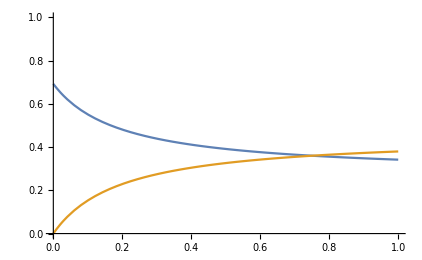

```mathematica
prs={d->4,n->4,μ->0.1}
Plot[{qinm/.prs,qoutm/.prs},{m,0,1},PlotRange->{0,1}]
```

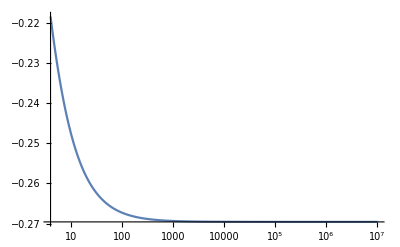

```mathematica
LogLinearPlot[βBD/.{Qin->QinM,Qout->QoutM}/.mychange/.{n->4,μ->0.1,m->0.1,p->0.45},{d,4,10000000},PlotRange->All]
```

### WF

#### In

```mathematica
qinwf=QinWF/.mychange//FullSimplify
```

(-d+(-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2))/(d (-1+n)+(-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2))

```mathematica
M1=(-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2);
M2=1/(2 μ-μ^2);
```

```mathematica
(-d + M1+M2)/((n-1)d+M1+M2);
qinwf-%//FullSimplify
```

0

```mathematica
M1
```

(-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)

```mathematica
M1s=(d-1)/(1-((d (1-m)-1)^2 (1-μ)^2)/(d-1)^2);
M1-M1s//FullSimplify
```

0

```mathematica
Limit[QinWF,μ->0]
Limit[qinwf,μ->0]
```

1

1

```mathematica
Limit[QinWF,d->∞]
Limit[qinwf,d->∞]//FullSimplify
```

((din^2-2 din dself+dself^2-(-1+m)^2) (-1+μ)^2)/(-1+2 m-m^2-2 m n+m^2 n+din^2 (-1+μ)^2-2 din dself (-1+μ)^2+dself^2 (-1+μ)^2+2 μ-4 m μ+2 m^2 μ-2 n μ+4 m n μ-2 m^2 n μ-μ^2+2 m μ^2-m^2 μ^2+n μ^2-2 m n μ^2+m^2 n μ^2)

-((-1+m)^2 (-1+μ)^2)/(-1-2 m (-1+n) (-1+μ)^2+m^2 (-1+n) (-1+μ)^2+(-1+n) (-2+μ) μ)

#### Out

```mathematica
qoutwf=QoutWF/.mychange//FullSimplify
```

(-1/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2))/(d (-1+n)+(-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2))

```mathematica
(-1/(d-1)M1+M2)/(d(n-1)+M1+M2)
%-qoutwf//FullSimplify
```

(-1/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2))/(d (-1+n)+(-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2))

0

```mathematica
ExportForR[x_]:=Module[{xx},xx=x/.{μ->mu,d->ndemes};xx]
```

```mathematica
ExportForR[qinm]
```

-((-1+mu) (mu-mu ndemes+m (-1+mu ndemes)))/(-mu (1+mu (-1+n)) (-1+ndemes)+m (-1+mu) (1+mu (-1+n) ndemes))

#### Export to R

Rewrite the Greek letters

```mathematica
GreekTerms={ω->sel, μ->mut}
```

{ω→sel,μ→mut}

Common parts to all functions

```mathematica
FunctionPartB=" <- function(p, sel, mut, m, g, n, d, Idself, Ieself){
## Arguments:
#  p   mutation bias
#  sel intensity of selection
#  mut mutation probability
#  m   emigration probability
#  g   proportion of interactions out of the group (interaction equivalent of m)
#  n   deme size
#  d   number of demes
#  Idself whether reproduction in site where the parent is
#  Ieself whether interactions with oneself
return(
";
FunctionPartE=")
}";
```

Function to translate Mathematica to R

```mathematica
ToRForm[x_]:=ToString[x/.GreekTerms//CForm]
```

Do it for Q

```mathematica
RtxtQinM="QinM "<>FunctionPartB<>ToRForm[QinM/.genericde//FullSimplify]<>FunctionPartE;
RtxtQoutM="QoutM "<>FunctionPartB<>ToRForm[QoutM/.genericde//FullSimplify]<>FunctionPartE;
RtxtQinWF="QinWF "<>FunctionPartB<>ToRForm[QinWF/.genericde//FullSimplify]<>FunctionPartE;
RtxtQoutWF="QoutWF "<>FunctionPartB<>ToRForm[QoutWF/.genericde//FullSimplify]<>FunctionPartE;
```

Define Power function in R

```mathematica
PowerDef="Power <- function(a,b) return(a^b)";
```

Combine all texts

```mathematica
Rtxt=PowerDef<>"

"<>RtxtQinM<>"

"<>RtxtQoutM<>"

"<>RtxtQinWF<>"

"<>RtxtQoutWF;
```

Export to txt file (Mathematica did not want R)

```mathematica
Export["Documents/Work/Projects/2016_SocEvolSubdivPop/Programs/Mathematica/analyticsQ.txt",Rtxt]
```

Documents/Work/Projects/2016_SocEvolSubdivPop/Programs/Mathematica/analyticsQ.txt

Convert the file extension to R

```mathematica
<<"!mv Documents/Work/Projects/2016_SocEvolSubdivPop/Programs/Mathematica/analyticsQ.txt Documents/Work/Projects/2016_SocEvolSubdivPop/Programs/Mathematica/analyticsQ.R"
```